# Settings

```mathematica
EigensystemSorted[H_,ρ_?NumericQ,ϕ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[H[ρ,ϕ]];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,Map[Normalize,eig]}
]
```

```mathematica
endif[H_,{x_?NumericQ,y_?NumericQ},bottomlevel_]:=Module[{e},
e=Sort@N@Eigenvalues[H[x,y]];
e[[bottomlevel+1]]-e[[bottomlevel]]]
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
(*chevron plot markers*)(*V shape: \/(lower-level DPs)*)vMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,1},{0,0},{1,1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
(* ∧shape: /\  (upper-level DPs)*)uMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,-1},{0,0},{1,-1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
plus=Graphics[{Line[{{-√2,0},{√2,0}}],Line[{{0,-√2},{0,√2}}]}];
```

```mathematica
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
ResourceFunction["PlotGrid"];
```

```mathematica
MyBlue=RGBColor[0,0.4,1];
MyGreen=RGBColor[0,1,0];
MyRed=RGBColor[1,0,0];
MyViolet=RGBColor[128/255,0,128/255];
geodColor=RGBColor[0,0.7,0.7];
geodThickness=0.015;
infGray=GrayLevel[0.3];
fillGray=GrayLevel[0.92];
blobGray=GrayLevel[0.9];
```

# Qutrit in magnetic field

```mathematica
(*Spin-1 matrices*)
Sx=1/Sqrt[2] {{0,1,0},{1,0,1},{0,1,0}};
Sy=1/Sqrt[2] {{0,-I,0},{I,0,-I},{0,I,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};

(*Full spin-1 Hamiltonian with zero-field splitting*)
(*Following NV center convention from [Rondin14]*)
```

```mathematica
HSpinFull[Bx_,By_,Bz_,D_,E_,μB_,g_]:=D*Sz.Sz+E*(Sx.Sx-Sy.Sy)+g μB(Bx*Sx+By*Sy+Bz*Sz)//Simplify
```

```mathematica
Chop@HSpinFull[Bx,By,Bz,d,e,μB,g]//MatrixForm
```

(d+Bz g μB | ((Bx-ⅈ By) g μB)/(√2) | e
((Bx+ⅈ By) g μB)/(√2) | 0 | ((Bx-ⅈ By) g μB)/(√2)
e | ((Bx+ⅈ By) g μB)/(√2) | d-Bz g μB)

```mathematica
H[Bx_,Bz_]:=HSpinFull[Bx,0,Bz,d,e,μB,g] (*multiply by 1000 to use mT as units of B*)
```

#### Exact root finding

```mathematica
ens=Eigenvalues[H[0,y]]
```

{0,d-√(e^2+g^2 y^2 μB^2),d+√(e^2+g^2 y^2 μB^2)}

```mathematica
sol=Quiet@Solve[ens[[1]]==ens[[2]],y]
root=sol[[2]]
```

{{y→-(√(d^2-e^2))/(g μB)},{y→(√(d^2-e^2))/(g μB)}}

{y→(√(d^2-e^2))/(g μB)}

```mathematica
ens/.y->0
```

{0,d-√(e^2),d+√(e^2)}

So the energy gap is 2e.

#### Plotting

```mathematica
d=2.87;      (* GHz-zero-field splitting*)
e=0.5;            (* e~100 kHz for high purity chemical vapour deposition grown diamond samples, but we need 0 to get exact crossing*)
μB=14;    (*GHz/T-effective gyromagnetic parameter*)
g=2 ;(*Landé g-factor*)

Chop@H[Bx,Bz]//MatrixForm
endif1[y_?NumericQ]:=Module[{sp},
sp=Sort[Eigenvalues[N@H[0,y]]];
sp[[2]]-sp[[1]]
]
```

(2.87+28 Bz | 14 √2 Bx | 0.5
14 √2 Bx | 0 | 14 √2 Bx
0.5 | 14 √2 Bx | 2.87-28 Bz)

```mathematica
yroot=N[y/.root,43]
```

0.100933

```mathematica
{Bz0,Bz1,Bz2}={0,2yroot,yroot}; (*needed for shifts later*)
```

```mathematica
(*conversion from radial to shifted radial, which will be used mainly for geometry*)
r[R_]:=RealSign[R-1/2](R-1/(4R))
ϕ[R_,Φ_]:=UnitStep[R-1/2]Φ+UnitStep[1/2-R](Φ+π)
HASR[H_,R_,Φ_]:=H[r[R],ϕ[R,Φ]]//FullSimplify
```

```mathematica
SRToR[{R_,Φ_}]:={r[R],Mod[ϕ[R,Φ],2π]}(*shifted radial to radial*)
RToSRIn[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (-r+√(1+r^2));
Φ=Mod[ϕ-π,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
RToSROut[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (r+√(1+r^2));
Φ=Mod[ϕ,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
SCToSR[X_,Y_]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
CToR[x_,y_]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)
RToC[r_,φ_]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
(*vector versions*)
SCToSR[{X_,Y_}]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
SRToSC[{R_,Φ_}]:={R Cos[Φ],R Sin[Φ]}; (*shifted radial to shifted cartesian*)
RToC[{r_,φ_}]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
CToR[{x_,y_}]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)
```

# Dirac string

## Basic functions and settings

#### Lie algebra generators

```mathematica
pauli=PauliMatrix[#]&/@Range[3];
gellMann={{{0,1,0},{1,0,0},{0,0,0}},{{0,-I,0},{I,0,0},{0,0,0}},{{1,0,0},{0,-1,0},{0,0,0}},{{0,0,1},{0,0,0},{1,0,0}},{{0,0,-I},{0,0,0},{I,0,0}},{{0,0,0},{0,0,1},{0,1,0}},{{0,0,0},{0,0,-I},{0,I,0}},(1/Sqrt[3])*{{1,0,0},{0,1,0},{0,0,-2}}};
gellMann4={(*λ₁ through λ₈-first 8 matrices*){{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-I,0,0},{I,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{0,0,-I,0},{0,0,0,0},{I,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,-I,0},{0,I,0,0},{0,0,0,0}},(1/Sqrt[3])*{{1,0,0,0},{0,1,0,0},{0,0,-2,0},{0,0,0,0}},(*λ₉ through λ₁₅-additional seven matrices*){{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}},{{0,0,0,-I},{0,0,0,0},{0,0,0,0},{I,0,0,0}},{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,-I},{0,0,0,0},{0,I,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,-I},{0,0,I,0}},(1/Sqrt[6])*{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-3}}};
```

#### Raw eigenvectors

```mathematica
Options[EigenvaluesAt]={"EigenvaluesFunction"->Automatic};

(*Get sorted eigenvalues at a parameter point.If "EigenvaluesFunction"->f is given,it uses f[params] instead of Eigenvalues.*)
EigenvaluesAt[H_,params___,OptionsPattern[]]:=Module[{evf=OptionValue["EigenvaluesFunction"],mat},
If[evf===Automatic,mat=H[params];
Sort@N@Eigenvalues[mat],
Sort@evf[params]
]];

(*Pick the n-th (sorted) eigenvalue at params*)
EigenvalueAt[H_,params___,Level_Integer:1,opts:OptionsPattern[EigenvaluesAt]]:=EigenvaluesAt[H,params,opts][[Level]];

(*Energy gap between level Level and Level+1 at params*)
eGap[H_,Level_Integer:1,params___,opts:OptionsPattern[EigenvaluesAt]]:=With[{e=EigenvaluesAt[H,params,opts]},e[[Level+1]]-e[[Level]]];

(*Unnormalized gauge-fixed eigenvector representative
-H: Hamiltonian matrix,
 -params:the parameter values (any arity),
 -w:a seed vector (same length as the Hilbert space dimension),
 -"Level"->n (default 1=ground state in sorted order),
 -"EigenvaluesFunction"->f (optional),where f[params] returns the numerical list of eigenvalues*)
Options[RawEigenvec]={"Level"->1,"EigenvaluesFunction"->Automatic};
RawEigenvec[H_,params___,w_,OptionsPattern[]]:=Module[{mat,λ,M},mat=H[params];
λ=EigenvalueAt[H,params,OptionValue["Level"],"EigenvaluesFunction"->OptionValue["EigenvaluesFunction"]];
M=mat-λ IdentityMatrix[Length@mat];
Adjugate[M].w
];
```

### Models

```mathematica
$Assumptions={x∈Reals,y∈Reals,z∈Reals};
```

## 2-level test

```mathematica
Clear[x,y,z]
```

```mathematica
dd={x,y,z};
H2[x_,y_,z_]=dd.pauli
```

{{z,x-ⅈ y},{x+ⅈ y,-z}}

Upper (Plus, has nodal line down from DP) and lower (Minus, has nodal line up from DP) hemisphere gauges for g.s. and 1.s. eigenvectors

```mathematica
v0P[x_,y_,z_]={x-I y,-(Norm[dd]+z)}//Simplify;
v1P[x_,y_,z_]={Norm[dd]+z,x+I y}//Simplify;
v0M[x_,y_,z_]={-(Norm[dd]-z),x+I y}//Simplify;
v1M[x_,y_,z_]={x-I y,Norm[dd]-z}//Simplify;
```

```mathematica
e0[x_,y_,z_]=-Norm[dd]//Simplify;
e1[x_,y_,z_]=Norm[dd]//Simplify;
```

```mathematica
ee[x_,y_,z_]:={e0[x,y,z],e1[x,y,z]}
```

```mathematica
(H2[x,y,z]-e0[x,y,z]IdentityMatrix[2]).v0P[x,y,z]//Simplify
(H2[x,y,z]-e1[x,y,z] IdentityMatrix[2]).v1P[x,y,z]//Simplify
(H2[x,y,z]-e0[x,y,z] IdentityMatrix[2]).v0M[x,y,z]//Simplify
(H2[x,y,z]-e1[x,y,z] IdentityMatrix[2]).v1M[x,y,z]//Simplify
```

{0,0}

{0,0}

{0,0}

«1 more identical outputs»

```mathematica
v0Raw[x_,y_,z_]:=RawEigenvec[H2,x,y,z,{1,0},"EigenvaluesFunction"->ee]
```

```mathematica
v0Raw[x,y,z]
```

{-z+√(x^2+y^2+z^2),-x-ⅈ y}

## Real symmetry: section y=0

For the real system, the Berry phase around DP has to be multiple of π, thus in the real gauge there has to be jump in the wavefunction . The point of this jump has to be consistent with the location of nodal line.

```mathematica
H2R[x_,z_]=H2[x,0,z];
```

```mathematica
v0PR[x_,z_]=v0P[x,0,z];
v1PR[x_,z_]=v1P[x,0,z];
v0MR[x_,z_]=v0M[x,0,z];
v1MR[x_,z_]=v1M[x,0,z];
```

```mathematica
eR[x_,z_]:=ee[x,0,z]
```

```mathematica
v0RRaw[x_,z_,Level_,w_]:=RawEigenvec[H2R,x,z,w,"EigenvaluesFunction"->eR ,"Level"->Level]
```

### We make a Gauge choice and solve analytically

```mathematica
ϕ=π/3;
w2={Cos[ϕ],Sin[ϕ]};
```

```mathematica
{v0RRaw1,v0RRaw2}=Simplify@Norm@v0RRaw[x,z,#,w2]&/@{1,2}
```

{√(2 x^2-√3 x √(x^2+z^2)+z (2 z+√(x^2+z^2))),√(2 x^2+2 z^2+√3 x √(x^2+z^2)-z √(x^2+z^2))}

```mathematica
Reduce[v0RRaw1==0,{x,z},Reals]
Reduce[v0RRaw2==0,{x,z},Reals]
```

x≥0&&z==-x/(√3)

x≤0&&z==-x/(√3)

### Numerical solution

```mathematica
ϕ=π/2;
w2={Cos[ϕ],Sin[ϕ]};
val[level_?IntegerQ][x_?NumericQ,z_?NumericQ]:=N@Norm@v0RRaw[x,z,level,w2];
```

```mathematica
{eigenvaluesAn,eigenvectorsAn}=Eigensystem[H2R[x,y],Cubics->True]//Simplify
```

{{-√(x^2+y^2),√(x^2+y^2)},{{(y-√(x^2+y^2))/x,1},{(y+√(x^2+y^2))/x,1}}}

```mathematica
eigenvectors3[x_,y_]=eigenvectorsAn;
```

```mathematica
{xmin,xmax}={-2.5,2.5};
{zmin,zmax}={-2.5,2.5};
precision=50;
imageresolution=300; 

powerRescale[t_]:=If[t<=Pi/4,(t/(π/4))^(1/2) π/4(*green->black*),π/4+((t-π/4)/(π/4)) π/4              (*black->white*)];

(*Full pipeline v->Blend parameter*)
compositeScale[v_]:=powerRescale[ArcTan[v]];

colorizer[v_]:=Blend[{{0,Green},{Pi/8,Black},{Pi/2,White}},compositeScale[v]];

(*Colorbar must use the same piecewise rescaling so it matches the plot*)
baseGradient=Blend[{{0,Green},{Pi/8,Black},{Pi/2,White}},powerRescale[#]]&;

(*Define the exact ArcTan angles for the colorbar ticks with MaTeX formatting*)
customTicks={{0,"0"},{Pi/4,"π/4"},{Pi/2-0.001,"π/2"}};

leg=BarLegend[{baseGradient,{0,Pi/2}},LegendMarkerSize->{12,90},Ticks->customTicks];
```

```mathematica
linesThickness=0.015;
(*3. Texture Generation*)
makeTexture[level_]:=Module[{basePlot,lines},basePlot=DensityPlot[val[level][x,z],{x,xmin,xmax},{z,zmin,zmax},ColorFunction->colorizer,ColorFunctionScaling->False,PlotPoints->precision,PlotRangePadding->None,Frame->False,Axes->False];
lines=If[level==1,Graphics[{Thickness[linesThickness],Darker@geodColor,Circle[{0,-1},1],Thickness[linesThickness],Dashing[Large],Darker@MyViolet,Circle[{0,-1},1]}],Graphics[{Thickness[linesThickness],Darker@geodColor,Circle[{0,-1},1],Thickness[linesThickness],Dashing[Large],Darker@MyViolet,Circle[{0,1},1]}]];
Rasterize[Show[basePlot,lines],ImageResolution->imageresolution]];

tex1=makeTexture[1];
tex2=makeTexture[2];

(*4. 3D Sheet Function*)sheet[level_,style_,tex_]:=ParametricPlot3D[{x,z,eR[x,z][[level]]},{x,xmin,xmax},{z,zmin,zmax},PlotStyle->Directive[style,Texture[tex]],TextureCoordinateFunction->({#4,#5}&),TextureCoordinateScaling->True,MeshFunctions->{#3&,(ArcTan[#2,#1]&)},Mesh->{5,3 4-1},Lighting->"Neutral",MeshStyle->Opacity[0.2],PlotPoints->precision,MaxRecursion->2,PerformanceGoal->"Quality",ViewPoint->{1.3,-2,1.}];

(*5. Build and Display*)
p1=sheet[1,Opacity[0.8],tex1];
p2=sheet[2,Opacity[0.8],tex2];

(*CRITICAL FIX:Domain restored to {0,Pi/2} to match customTicks*)
leg=BarLegend[{baseGradient,{0,Pi/2}},LegendLabel->"atan(||Ψ||)",LegendMarkerSize->{10,172},Ticks->customTicks];

plot2d=Show[Legended[Show[p1,p2],Placed[leg,{1,0.5}]],AxesLabel->{"x","z","E"},PlotRange->All,BoxRatios->{1,1,1/2},ImageSize->340,Ticks->{Range[-4,4,2],Range[-4,4,2],Range[-2,2,2]}];

Rasterize[plot2d,RasterSize->600]
```

-Graphics-

### Circular paths in extended coordinates

In shifted radial coordinates the DP is circle with R=1/2

```mathematica
circle=Graphics[{EdgeForm[{MyRed,Thick,Dashed}],FaceForm[Opacity[0.08],Black],Disk[{0,0},1/2]}];
```

We transform from Cartesian circle to radial, to shifted radial, to shifted Cartesian (just because these functions were easy to write) and get:

```mathematica
X1[t_]:=-{Sin[t],Cos[t]+1};
```

```mathematica
X2[t_]:=Which[
0<=t<π,-{Sin[t],Cos[t]+1},
π<=t<3 π,-{Sin[-t-π],Cos[-t-π]-1},
3 π<=t<4 π,-{Sin[t],Cos[t]+1}]
X1[t_]:=-{Sin[t],Cos[t]+1};
```

Path on the manifold M0 to DP, using which it tunnels to M1

```mathematica
p1=ParametricPlot[SRToSC@RToSROut@CToR@X1[t],{t,0,π},PlotStyle->geodColor,PlotLegends->Automatic,AspectRatio->1];
p1P=ParametricPlot[SRToSC@RToSROut@CToR@X2[t],{t,0,π},PlotStyle->{MyViolet,Dashed,Thickness[0.01]},PlotLegends->Automatic,AspectRatio->1];
```

path from DP to the same DP on M1

```mathematica
p2=ParametricPlot[SRToSC@RToSRIn@CToR@X1[t],{t,π+10^-15,3π},PlotStyle->geodColor,PlotLegends->Automatic,AspectRatio->1];p2P=ParametricPlot[SRToSC@RToSRIn@CToR@X2[t],{t,π+10^-15,3π},PlotStyle->{MyViolet,Dashed,Thickness[0.01]},PlotLegends->Automatic,AspectRatio->1];
```

after tunneling to M0, the path continues to the initial point

```mathematica
p3=ParametricPlot[SRToSC@RToSROut@CToR@X1[t],{t,3π+10^-15,4π},PlotStyle->geodColor,PlotLegends->Automatic,AspectRatio->1];p3P=ParametricPlot[SRToSC@RToSROut@CToR@X2[t],{t,3π+10^-15,4π},PlotStyle->{MyViolet,Dashed,Thickness[0.01]},PlotLegends->Automatic,AspectRatio->1];
```

```mathematica
darkblue=RGBColor[0.121569,0.00784314,0.396078];
pNodal=ListLinePlot[{{0,0},{0,-2.3}},PlotStyle->{Darker@Green}];
pNodal2=ListLinePlot[{{0,0},{Sin[π/5],Cos[π/5]}},PlotStyle->{Darker@Green,Dotted}];
```

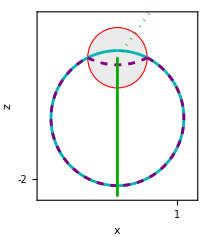

```mathematica
plot2dLines=Show[{circle,p1,p2,p3,p1P,p2P,p3P,pNodal,pNodal2},PlotRange->{{-1.3,1.3},{-2.3,0.7}},Frame->True,FrameLabel->{"x","z"},FrameTicks->{{Range[-5,5,1],None},{Range[-5,5,1],None}}]
```

## 3-level

```mathematica
H3[Bx_,Bz_]:=HSpinFull[Bx,0,Bz,d,e,μB,g]
```

### We make a Gauge choice and solve analytically

```mathematica
{eigenvaluesAn,eigenvectorsAn}=Eigensystem[H3[x,y],Cubics->True]//Simplify;
```

```mathematica
order={2,3,1};
```

```mathematica
eigenvectors3[x_,y_]=eigenvectorsAn[[#]]&/@order;
```

```mathematica
eigenvalues3[x_,y_]=Re[eigenvaluesAn[[#]]&/@order//Simplify];
```

```mathematica
Chop@eigenvalues3[2.,1.]
```

{-60.712,1.89634,64.5557}

```mathematica
v3Raw[x_,y_,Level_,w_]:=RawEigenvec[H3,x,y,w,"EigenvaluesFunction"->eigenvalues3 ,"Level"->Level]
```

```mathematica
w2={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}; (*gauge choice*)
```

### 3D plots

```mathematica
{xmin,xmax}={-0.25,0.25};
{ymin,ymax}={-0.25,0.25};
```

```mathematica
(*plot a*)
precision=60;
θ=2;
ϕ=0;
w2=N@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
val[level_?IntegerQ][x_?NumericQ,y_?NumericQ]:=N@Norm@v3Raw[x,y,level,w2];
```

{0.909297,0.,-0.416147}

```mathematica
(*Piecewise rescaling power only on black->white segment*)
powerRescale[t_]:=If[t<=Pi/4,t,(*green->black:unchanged*)π/4+((t-π/4)/(π/4))^3 π/4              (*black->white:1/3 power*)];

(*Full pipeline v->Blend parameter*)
compositeScale[v_]:=powerRescale[ArcTan[v]];

colorizer[v_]:=Blend[{{0,Green},{Pi/4,Black},{Pi/2,White}},compositeScale[v]];

(*Colorbar must use the same piecewise rescaling so it matches the plot*)
baseGradient=Blend[{{0,Green},{Pi/4,Black},{Pi/2,White}},powerRescale[#]]&;

(*Define the exact ArcTan angles for the colorbar ticks with MaTeX formatting*)
customTicks={{0,"0"},{Pi/4,"π/4"},{Pi/2-0.001,"π/2"}};

leg=BarLegend[{baseGradient,{0,Pi/2}},LegendMarkerSize->{12,100},Ticks->customTicks];
```

```mathematica
(*plot a itself*)
With[{xs=Subdivide[xmin,xmax,precision],ys=Subdivide[ymin,ymax,precision]},vals=Flatten@ParallelTable[val[lev][x,y],{lev,{1,2,3}},{x,xs},{y,ys}]];

sheet[level_,style_]:=ParametricPlot3D[{x,y,eigenvalues3[x,y][[level]]},{x,xmin,xmax},{y,ymin,ymax},Boxed->False,Axes->False,PlotStyle->style,MeshFunctions->{#3+1&,(Cos[6 ArcTan[#2,#1]]&)},Mesh->{5,{0}},MeshStyle->Opacity[0.1],ColorFunctionScaling->False,ColorFunction->Function[{xx,yy,EE},colorizer[val[level][xx,yy]]],PlotPoints->precision,MaxRecursion->2,PerformanceGoal->"Quality",ViewPoint->{6.5,3,3.}];

p1=sheet[1,Directive[Opacity[0.9]]];
p2=sheet[2,Directive[Opacity[0.6]]];
p3=sheet[3,Directive[Opacity[0.2]]];

mkCross[color_,pt3D_,size_]:={color,Thick,Inset[Graphics[{color,AbsoluteThickness[2],Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]},PlotRange->1.2 {{-1,1},{-1,1}},ImageSize->30],pt3D,Center,{size,size}]}

mkPlus[color_,pt3D_,size_]:={color,Thick,Inset[Graphics[{color,AbsoluteThickness[2],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]},PlotRange->1.2 {{-1,1},{-1,1}},ImageSize->30],pt3D,Center,{size,size}]}


Show[Legended[Show[p1,p2,p3],Placed[leg,{1,0.5}]],PlotRange->All,BoxRatios->{1,1,0.9}]
```

-Graphics-

### 2D plots

```mathematica
markersize=0.12;
bgDP0Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{uMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{uMarker,markersize}]]
bgDP1Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{vMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{vMarker,markersize}]]
bgDP2Cart:=Graphics[]
```

```mathematica
Quiet@ResourceFunction["PlotGrid"][{Module[{w2,val,θ=2,φ=0,levels={1,2,3},xs,zs,samples=precision,tableVals,plots},w2={Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]};
val[level_?IntegerQ][x_?NumericQ,z_?NumericQ]:=N@Norm@v3Raw[x,z,level,w2];
{xs,zs}={Subdivide[-0.25,0.25,samples],Subdivide[-0.25,0.25,samples]};
tableVals=Quiet@ParallelTable[val[l][x,z],{l,levels},{z,zs},{x,xs}];
plots=MapThread[Function[{l,k},Module[{ldp},ldp=ListDensityPlot[tableVals[[l]],DataRange->{{-0.25,0.25},{-0.25,0.25}},ColorFunctionScaling->False,ColorFunction->(colorizer[#]&),FrameLabel->{"B_x","B_z"}];
Show[ldp,{bgDP0Cart,bgDP1Cart,bgDP2Cart}[[l]]]]],{levels,{0,1,2}}];
plots]}]
```

-Graphics-